# Time series analysis

## Auxiliary functions

### correlationPlots

```mathematica
ClearAll[correlationPlots]

Options[correlationPlots] = Flatten[{
	"Lags" -> 20
}];

correlationPlots[data_TemporalData, opts: OptionsPattern[]] :=
Module[
	{thisData},
	thisData = data["Values"];
	If[
		MatchQ[thisData, _StructuredArray],
		thisData = QuantityMagnitude[thisData] 
	];
	correlationPlots[thisData, opts]
]

correlationPlots[data: {__?NumericQ}, opts: OptionsPattern[]] :=
correlationPlots[data, Length[data], opts]

correlationPlots[model_, dataPoints_, opts: OptionsPattern[]] :=
Module[
	{
		lags, 
		data,
		linePlot, acfPlot, pacfPlot
	},
	lags = OptionValue["Lags"];
	
	data = 
	Switch[
		model,
		_?(!StringFreeQ[ToString[Head[#]], "Process"] &), RandomFunction[model, {1, dataPoints}],
		_, model
	];
	
	linePlot =
	ListLinePlot[
		data,
		Frame->True,
		PlotRange->All,
		AspectRatio->1/(2GoldenRatio),
		GridLines->Automatic,
		GridLinesStyle->Directive[{Thickness[.001],LightGray}],
		ImageSize->Scaled[1.]
	];
	
	acfPlot =
	DiscretePlot[
		CorrelationFunction[data, h], {h, 1, lags},
		Epilog -> {
			Dashed,
			Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],
			Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
		},
		PlotLabel->"ACF",
		ExtentSize->.5,
		PlotRange->{Automatic,{-1,1}},
		ImageSize->Scaled[.49]
	];
	
	pacfPlot =
	DiscretePlot[
		PartialCorrelationFunction[data,h],{h, 1, lags},
		Epilog -> {
			Dashed,
			Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],
			Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
		},
		PlotLabel->"PACF",
		ExtentSize->.5,
		PlotRange->{Automatic,{-1,1}},
		ImageSize->Scaled[.49]
	];
	
	Column[
		{
			linePlot,
			Spacer[1],
			Row[{acfPlot, pacfPlot}]
		}
	]
]
```

### summaryHistogram

```mathematica
ClearAll[summaryHistogram]

summaryHistogram[values_, binSize_] :=
Module[
	{
		mean, std, skewness, kurtosis,
		histogram, grid
	},
	{mean, std, skewness, kurtosis} = Through[{Mean, StandardDeviation, Skewness, Kurtosis}[values]];
	
	histogram = Histogram[values, binSize, "Probability", ImageSize -> Scaled[.5]];
	grid = Grid[
		{
			{Mean, StandardDeviation, Skewness, Kurtosis},
			{mean, std, skewness, kurtosis}
		},
		ItemSize -> 10,
		Frame -> All,
		FrameStyle -> Directive[{LightGray, Opacity[.5]}],
		BaseStyle -> {FontFamily -> "Helvetica"}
	];
	
	Framed[#, RoundingRadius -> 5, FrameStyle -> LightGray] & @
	Column[
		{
			histogram,
			grid
		},
		Alignment -> Center,
		Spacings -> 1.5
	]
]
```

## Electrical Load Data

```mathematica
loadTimeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
loadTraining =TimeSeries[TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2012,9,28}],DateObject[{2019,6,1}]}]];
loadTest=TimeSeries[TimeSeriesWindow[loadTimeSeriesResampled,{DateObject[{2019,6,2}],DateObject[{2019,6,8}]}]];
```

### Pipeline

#### Plot the data!

```mathematica
plot=
DateListPlot[
loadTraining ,
FrameLabel->Automatic,
PlotRange->All,
AspectRatio->1/(2GoldenRatio),
GridLines->Automatic,
GridLinesStyle->Directive[{Thickness[.0001],LightGray}],
ImageSize->Large,
Mesh->All,
PlotMarkers->Graphics[{EdgeForm[{Thick,ColorData[97][1]}],White,Disk[{0,0},Scaled[.015]]}]
]
```

#### Is there a trend?

```mathematica
loadTraining ["Properties"]
```

{DatePath,Dates,FirstDate,FirstTime,FirstValue,LastDate,LastTime,LastValue,Path,PathFunction,PathLength,Times,ValueDimensions,Values}

```mathematica
values=N@TimeSeriesMap[QuantityMagnitude,loadTraining ]["Values"]
```

{11641.4,10883.1,10707.6,10663.2,10627.7,10848.8,11520.7,12877.6,14087.2,14646.6,14992.9,15267.5,15400.2,15361.9,15344.1,15176.5,15081.6,15134.4,15283.5,58474,9528.55,9547.94,10025.8,10412.2,10958.8,10999.2,10849.6,10863.,10889.4,11002.4,11263.1,11571.4,11965.6,12325.8,12536.9,12568.7,12682.3,12307.2,11450.3}
 |  |  |  |

```mathematica
linModel=LinearModelFit[values,t,t]
```

FittedModel[15022.2-0.0237626 t]

```mathematica
linModel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 15022.2 | 21.2424 | 707.179 | 0.
t | -0.0237626 | 0.000628802 | -37.7903 | 8.79571×10^-309

Estimated slope is compatible with 0.!

#### Is there a seasonal pattern?

Should we expect any seasonality?

Can we see any seasonality in the data?

```mathematica
plot
```

Look at the autocorrelation of the time series to search for the period of correlations:

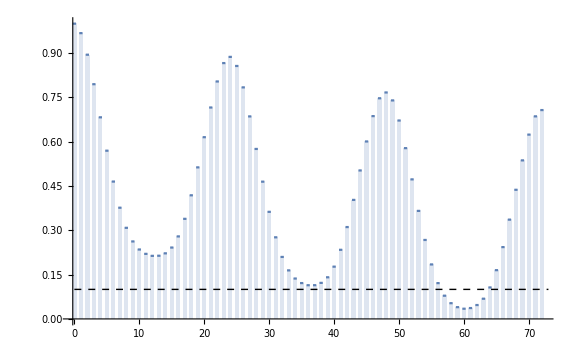

```mathematica
With[
{
data=values,
dataPoints=400,
lags=72
},
DiscretePlot[
CorrelationFunction[data,h],
{h,0,lags},
ExtentSize->.5,
PlotRange->All,
Epilog -> {
Dashed,
Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
},
ImageSize->Large
]
]
```

Let’s look at how much each hour deviates from the mean in average:

```mathematica
(* deviations from the mean *)
deviations=values-Mean[values]
```

{-2685.57,-3443.83,-3619.39,-3663.79,-3699.31,-3478.15,-2806.31,-1449.42,-239.765,58494,-3063.86,-2755.61,-2361.38,-2001.16,-1790.11,-1758.25,-1644.71,-2019.78,-2876.64}
 |  |  |  |

```mathematica
(* partition the data *)
partitionDeviations=Partition[deviations,24]
```

{{-2685.57,-3443.83,-3619.39,-3663.79,-3699.31,-3478.15,-2806.31,-1449.42,-239.765,6,849.505,754.595,807.425,956.555,1183.13,1116.37,514.925,-349.525,-1488.25},2437}
 |  |  |  |

```mathematica
(* gather the contributions for each hour *)
gatherDeviationsByHour=Transpose[partitionDeviations]
```

{1}
 |  |  |  |

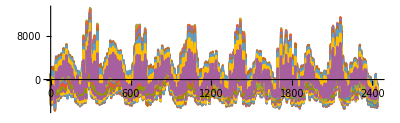

```mathematica
ListLinePlot[gatherDeviationsByHour,PlotStyle->Thick,AspectRatio->1/(2GoldenRatio),ImageSize->Scaled[.95],AxesOrigin->{1,Automatic},PlotLegends->Placed[Automatic,Bottom]]
```

```mathematica
(* mean deviation per hour *)
meanDeviationPerHour=Mean/@gatherDeviationsByHour
```

{-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47,-2125.09,-1367.91,-399.856,236.701,586.863,820.104,953.2,989.712,1023.76,1032.73,1074.33,1272.36,1711.94,2119.85,2125.,1838.4,1114.74,-25.9349}

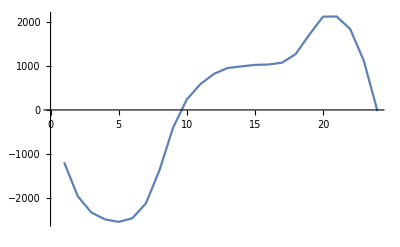

```mathematica
ListLinePlot[meanDeviationPerHour]
```

```mathematica
(* hourly deviations *)
seasonalityRules=Thread[Range[Length[meanDeviationPerHour]]->meanDeviationPerHour]
```

{1→-1191.39,2→-1962.39,3→-2332.04,4→-2487.46,5→-2545.13,6→-2462.47,7→-2125.09,8→-1367.91,9→-399.856,10→236.701,11→586.863,12→820.104,13→953.2,14→989.712,15→1023.76,16→1032.73,17→1074.33,18→1272.36,19→1711.94,20→2119.85,21→2125.,22→1838.4,23→1114.74,24→-25.9349}

```mathematica
{DateObject[{2012,9,28}],DateObject[{2019,6,1}]}
```

```mathematica
(* seasonality series *)
seasonalitySeries=Flatten[Table[Range[24],{QuantityMagnitude@DateDifference[DateObject[{2012,9,28}],DateObject[{2019,6,1}]]+1}]]/.seasonalityRules
```

{-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47,-2125.09,-1367.91,-399.856,58494,1032.73,1074.33,1272.36,1711.94,2119.85,2125.,1838.4,1114.74,-25.9349}
 |  |  |  |

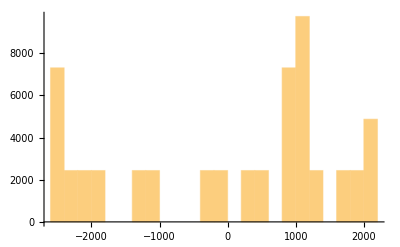

```mathematica
Histogram[seasonalitySeries]
```

```mathematica
Histogram[sea
```

Compare the average hourly deviation from the mean with the actual time series:

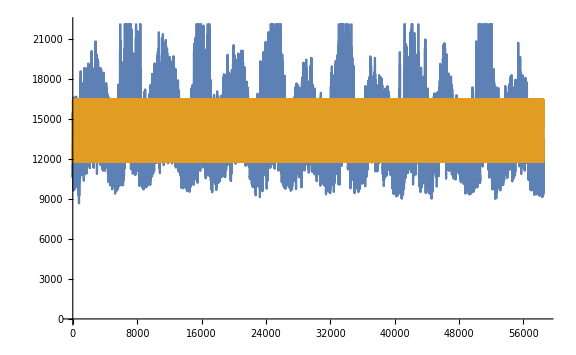

```mathematica
ListLinePlot[{values,seasonalitySeries+Mean[values]},Epilog:>{Thick,Dashed,Gray,Line[{{0,Mean[values]},{60,Mean[values]}}]},ImageSize->Large]
```

Compare the seasonally adjusted time series with the actual one:

```mathematica
values//Length
```

58512

```mathematica
Flatten[seasonalitySeries]//Length
```

58488

```mathematica
residuals=values-Mean[values]-Flatten[seasonalitySeries]
```

{-1494.18,-1481.44,-1287.35,-1176.34,-1154.18,-1015.69,-681.224,-81.5152,160.092,58494,-4096.59,-3829.95,-3633.74,-3713.1,-3909.96,-3883.25,-3483.11,-3134.53,-2850.71}
 |  |  |  |

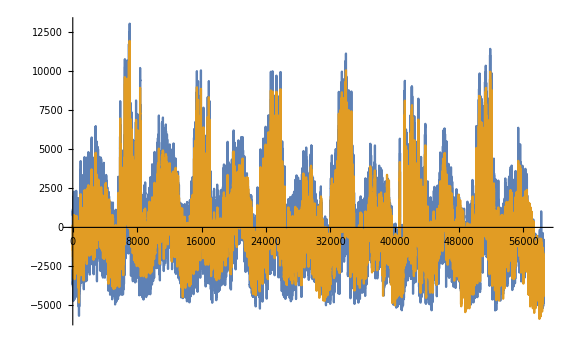

```mathematica
ListLinePlot[{values-Mean[values],residuals},ImageSize->Large,PlotRange->All]
```

Look at the distribution of the residuals:

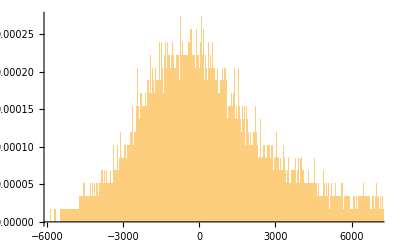
-Graphics-
Mean | StandardDeviation | Skewness | Kurtosis
-2.30793×10^-13 | 2060.34 | 0.898771 | 4.71529

```mathematica
summaryHistogram[residuals,{0.5}]
```

Do we still have any appealing pattern in the autocorrelation plot?

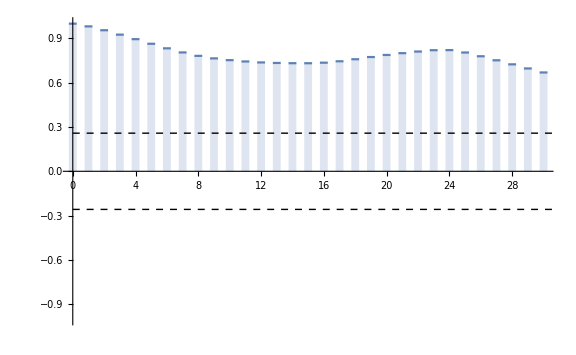

```mathematica
With[
{
data=residuals,
dataPoints=60,
lags=30
},
DiscretePlot[
CorrelationFunction[data,h],
{h,0,lags},
ExtentSize->.5,
PlotRange->{-1,1},
Epilog -> {
Dashed,
Line[{{0,2(dataPoints)^(-1/2)},{lags + 1, 2(dataPoints)^(-1/2)}}],Line[{{0,-2(dataPoints)^(-1/2)},{lags + 1, -2(dataPoints)^(-1/2)}}]
},
ImageSize->Large
]
]
```

#### Measure of the quality of our model

How well are we fitting the training data? Compare the sum of squares of the residuals to the variance of the data:

```mathematica
Total[(values-Mean[values])^2]
```

3.95626×10^11

```mathematica
Total[residuals^2]
```

2.48379×10^11

```mathematica
(* coefficient of determination: R^2 -> measure how much of the variance of the data that is captured by our model *)
rSquaredTraining=1-Total[residuals^2]/Total[(values-Mean[values])^2]
```

0.372188

#### Modelling the residuals

We saw above that the residuals are very well aproximated by a normal distribution with 0. mean and standard deviation 1.29, hence:

```mathematica
𝒟1=NormalDistribution[Mean[residuals],StandardDeviation[residuals]]
```

NormalDistribution[-2.30793×10^-13,2060.34]

Alternatively, we could estimate a probability distribution using a SmoothKernelDistribution:

```mathematica
𝒟2=SmoothKernelDistribution[residuals]
```

DataDistribution[…]

Another possibility yet would be to use the function FindDistribution which would try and find a known distribution that fits well the sample data:

```mathematica
FindDistribution[residuals,10,All,RandomSeeding->1234]
```

```mathematica
𝒟3=FindDistribution[residuals,RandomSeeding->1234]
```

MixtureDistribution[{0.788722,0.211278},{NormalDistribution[-798.785,1498.3],LogNormalDistribution[7.79416,0.690598]}]

Comparing the PDF’s generated by these different approachs:

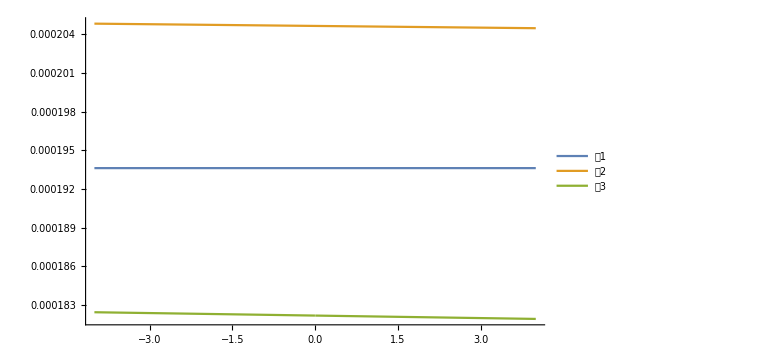

```mathematica
Plot[Evaluate[Table[PDF[dist][x],{dist,{𝒟1,𝒟2,𝒟3}}]],{x,-4,4},ImageSize->Large,PlotLegends->Placed[{"𝒟1","𝒟2","𝒟3"},Bottom],PlotRange->All]
```

#### Forecasting

We want the produce forecast for the period of Jan 2015 until Jun 2017, i.e. 30 months

```mathematica
forecastMean=Table[Mean[values],{30}]
```

{14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.,14327.}

```mathematica
forecastSeasonality=Take[Flatten[Table[Range[12],{3}]]/.seasonalityRules,30]
```

{-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47,-2125.09,-1367.91,-399.856,236.701,586.863,820.104,-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47,-2125.09,-1367.91,-399.856,236.701,586.863,820.104,-1191.39,-1962.39,-2332.04,-2487.46,-2545.13,-2462.47}

```mathematica
medianForecast=forecastMean+forecastSeasonality;
```

```mathematica
ClearAll[upperConfLimit]
upperConfLimit[dist_]:=forecastMean+forecastSeasonality+2StandardDeviation[dist]
```

```mathematica
ClearAll[lowerConfLimit]
lowerConfLimit[dist_]:=forecastMean+forecastSeasonality-2StandardDeviation[dist]
```

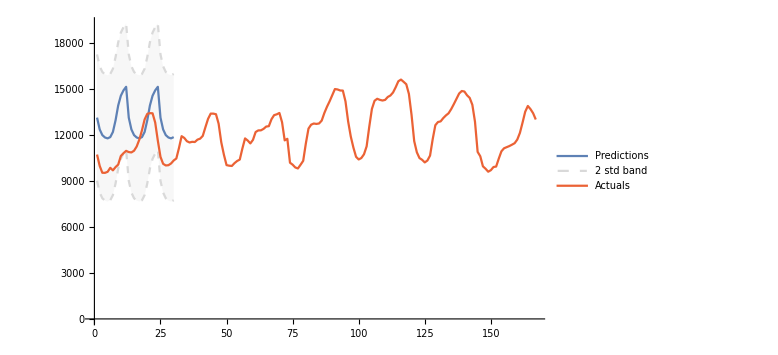

```mathematica
With[{dist=𝒟1},ListLinePlot[{medianForecast,upperConfLimit[dist],lowerConfLimit[dist],loadTest["Values"]},PlotStyle->{Automatic,Directive[{Dashed,LightGray}],Directive[{Dashed,LightGray}]},Filling->{2->{1},3->{1}},PlotLegends->{"Predictions","2 std band",None,"Actuals"},ImageSize->Large]]
```

#### Measure of the quality of our predictions

How well are we fitting the test data? Compare the sum of squares of the residuals to the variance of the data:

```mathematica
valuesTest=N@TimeSeriesMap[QuantityMagnitude,loadTest]["Values"];
```

```mathematica
residualsTest=medianForecast-valuesTest;
```

Thread::tdlen: Objects of unequal length in {13135.6,12364.6,11994.9,11839.5,11781.8,11864.5,12201.9,12959.1,13927.1,14563.7,«11»,14563.7,14913.8,15147.1,13135.6,12364.6,11994.9,11839.5,11781.8,11864.5}+{«1»} cannot be combined.

```mathematica
Total[(valuesTest-Mean[valuesTest])^2]
```

4.55021×10^8

```mathematica
Total[residualsTest^2]
```

Total[({13135.6,12364.6,11994.9,11839.5,11781.8,11864.5,12201.9,12959.1,13927.1,14563.7,14913.8,15147.1,13135.6,12364.6,11994.9,11839.5,11781.8,11864.5,12201.9,12959.1,13927.1,14563.7,14913.8,15147.1,13135.6,12364.6,11994.9,11839.5,11781.8,11864.5}+{-10725.1,-9986.71,-9537.01,-9532.71,-9600.07,-9861.06,-9694.89,-9908.36,-10070.,-10631.8,-10814.,-10967.4,-10887.1,-10865.,-10975.3,-11253.2,-11702.6,-12312.1,-13016.,-13380.,-13427.6,-13418.5,-12815.4,-11629.8,-10575.7,-10121.4,-10015.2,-10031.2,-10144.1,-10338.8,-10469.5,-11155.6,-11924.6,-11811.1,-11596.3,-11514.1,-11556.8,-11544.,-11698.4,-11762.3,-11944.3,-12509.1,-13053.3,-13397.2,-13396.7,-13357.2,-12737.6,-11525.2,-10713.1,-10036.5,-9999.02,-9982.02,-10163.8,-10305.6,-10397.7,-11127.2,-11779.8,-11641.9,-11451.7,-11685.8,-12195.8,-12300.7,-12306.3,-12401.3,-12552.3,-12578.,-13029.3,-13298.6,-13351.2,-13440.2,-12834.5,-11651.2,-11753.2,-10193.7,-10065.3,-9884.7,-9818.26,-10059.9,-10316.8,-11447.4,-12417.6,-12675.3,-12750.7,-12725.5,-12753.6,-12941.1,-13434.5,-13845.4,-14203.2,-14601.1,-15000.1,-14973.5,-14906.9,-14900.1,-14196.,-12892.1,-11904.5,-11177.3,-10580.2,-10405.2,-10499.3,-10743.1,-11259.9,-12545.3,-13705.,-14236.,-14365.5,-14296.1,-14252.5,-14293.2,-14482.7,-14580.4,-14776.6,-15118.8,-15508.8,-15618.6,-15471.7,-15314.3,-14679.1,-13308.3,-11604.5,-10873.1,-10495.7,-10382.3,-10212.9,-10337.6,-10658.3,-11729.,-12641.7,-12848.1,-12891.3,-13105.7,-13278.5,-13418.9,-13691.4,-14018.4,-14362.7,-14708.5,-14872.8,-14837.7,-14591.9,-14423.7,-13973.1,-12869.5,-10900.8,-10615.,-9958.89,-9799.72,-9606.37,-9705.22,-9911.85,-9943.31,-10459.4,-10937.6,-11135.7,-11208.1,-11279.6,-11370.,-11467.,-11703.2,-12140.8,-12811.6,-13519.9,-13896.4,-13691.6,-13421.6,-13012.8})^2]

```mathematica
rSquaredTest=1-Total[residualsTest^2]/Total[(valuesTest-Mean[valuesTest])^2]
```

1-2.1977×10^-9 Total[({13135.6,12364.6,11994.9,11839.5,11781.8,11864.5,12201.9,12959.1,13927.1,14563.7,14913.8,15147.1,13135.6,12364.6,11994.9,11839.5,11781.8,11864.5,12201.9,12959.1,13927.1,14563.7,14913.8,15147.1,13135.6,12364.6,11994.9,11839.5,11781.8,11864.5}+{-10725.1,-9986.71,-9537.01,-9532.71,-9600.07,-9861.06,-9694.89,-9908.36,-10070.,-10631.8,-10814.,-10967.4,-10887.1,-10865.,-10975.3,-11253.2,-11702.6,-12312.1,-13016.,-13380.,-13427.6,-13418.5,-12815.4,-11629.8,-10575.7,-10121.4,-10015.2,-10031.2,-10144.1,-10338.8,-10469.5,-11155.6,-11924.6,-11811.1,-11596.3,-11514.1,-11556.8,-11544.,-11698.4,-11762.3,-11944.3,-12509.1,-13053.3,-13397.2,-13396.7,-13357.2,-12737.6,-11525.2,-10713.1,-10036.5,-9999.02,-9982.02,-10163.8,-10305.6,-10397.7,-11127.2,-11779.8,-11641.9,-11451.7,-11685.8,-12195.8,-12300.7,-12306.3,-12401.3,-12552.3,-12578.,-13029.3,-13298.6,-13351.2,-13440.2,-12834.5,-11651.2,-11753.2,-10193.7,-10065.3,-9884.7,-9818.26,-10059.9,-10316.8,-11447.4,-12417.6,-12675.3,-12750.7,-12725.5,-12753.6,-12941.1,-13434.5,-13845.4,-14203.2,-14601.1,-15000.1,-14973.5,-14906.9,-14900.1,-14196.,-12892.1,-11904.5,-11177.3,-10580.2,-10405.2,-10499.3,-10743.1,-11259.9,-12545.3,-13705.,-14236.,-14365.5,-14296.1,-14252.5,-14293.2,-14482.7,-14580.4,-14776.6,-15118.8,-15508.8,-15618.6,-15471.7,-15314.3,-14679.1,-13308.3,-11604.5,-10873.1,-10495.7,-10382.3,-10212.9,-10337.6,-10658.3,-11729.,-12641.7,-12848.1,-12891.3,-13105.7,-13278.5,-13418.9,-13691.4,-14018.4,-14362.7,-14708.5,-14872.8,-14837.7,-14591.9,-14423.7,-13973.1,-12869.5,-10900.8,-10615.,-9958.89,-9799.72,-9606.37,-9705.22,-9911.85,-9943.31,-10459.4,-10937.6,-11135.7,-11208.1,-11279.6,-11370.,-11467.,-11703.2,-12140.8,-12811.6,-13519.9,-13896.4,-13691.6,-13421.6,-13012.8})^2]

### Predicting with the built-in tools

```mathematica
tsModel=TimeSeriesModelFit[values]
```

TimeSeriesModel[…]

```mathematica
tsModel["Properties"]
```

{ACFPlot,ACFValues,AIC,AICc,BIC,BestFit,BestFitParameters,CandidateModels,CandidateModelSelectionValues,CandidateSelectionTable,CandidateSelectionTableEntries,CovarianceMatrix,ErrorVariance,FitResiduals,ForecastStandardErrors,InformationMatrix,LjungBoxPlot,LjungBoxValues,ModelFamily,PACFPlot,PACFValues,ParameterConfidenceIntervals,ParameterTable,ParameterTableEntries,PredictionLimits,Properties,SBC,SelectionCriterion,StandardizedResiduals,TemporalData}

```mathematica
TimeSeriesForecast[tsModel,{30}]
```

TemporalData[…]

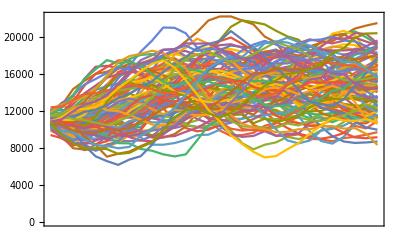

```mathematica
DateListPlot[RandomFunction[tsModel,{29},100]]
```

```mathematica
paths=RandomFunction[tsModel,{29},10000]
```

TemporalData[<<10000>>]

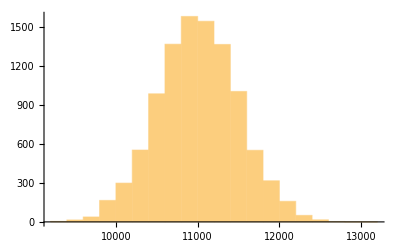

```mathematica
Histogram[test[[1]]]
```

```mathematica
test=Sort/@Transpose[paths["ValueList"]];
```

```mathematica
tsModelMedianForecast=#[[5000]]&/@(Sort/@Transpose[paths["ValueList"]])
```

{11000.1,10862.2,10979.5,11227.8,11574.4,11962.5,12360.7,12739.,13125.1,13455.6,13708.8,13969.2,14140.,14264.3,14343.8,14418.1,14475.8,14487.4,14491.1,14470.9,14474.9,14435.5,14426.5,14410.2,14406.4,14401.8,14380.6,14368.4,14342.4,14310.9}

```mathematica
tsModelUpperBandForecast=#[[9770]]&/@(Sort/@Transpose[paths["ValueList"]])
```

{11999.3,12674.7,13591.6,14529.7,15474.8,16343.7,17123.8,17755.6,18335.3,18772.8,19072.4,19379.8,19597.6,19702.4,19861.5,19873.5,19887.7,19884.9,19861.8,19810.8,19815.9,19832.6,19768.2,19763.4,19806.2,19821.4,19748.9,19694.3,19686.7,19657.7}

```mathematica
tsModelLowerBandForecast=#[[230]]&/@(Sort/@Transpose[paths["ValueList"]])
```

{10007.3,9119.75,8368.22,7874.86,7613.58,7529.07,7560.44,7735.14,7993.47,8214.46,8446.01,8599.09,8712.41,8923.35,9076.92,9093.82,9016.48,9017.13,9030.94,9061.61,9027.59,9070.64,9040.22,9012.19,9071.59,8999.72,8976.43,8899.43,8812.04,8824.89}

```mathematica
(* R^2 in the training data *)
tsModelR2Training=1-Total[(tsModel["FitResiduals"]["Values"])^2]/Total[(values-Mean[values])^2]
```

0.964874

```mathematica
(* R^2 in the test data *)
tsModelR2Test=1-Total[(tsModelMedianForecast-valuesTest)^2]/Total[(valuesTest-Mean[valuesTest])^2]
```

Thread::tdlen: Objects of unequal length in {11000.1,10862.2,10979.5,11227.8,11574.4,11962.5,12360.7,12739.,13125.1,13455.6,«11»,14435.5,14426.5,14410.2,14406.4,14401.8,14380.6,14368.4,14342.4,14310.9}+{«1»} cannot be combined.

1-2.1977×10^-9 Total[({11000.1,10862.2,10979.5,11227.8,11574.4,11962.5,12360.7,12739.,13125.1,13455.6,13708.8,13969.2,14140.,14264.3,14343.8,14418.1,14475.8,14487.4,14491.1,14470.9,14474.9,14435.5,14426.5,14410.2,14406.4,14401.8,14380.6,14368.4,14342.4,14310.9}+{-10725.1,-9986.71,-9537.01,-9532.71,-9600.07,-9861.06,-9694.89,-9908.36,-10070.,-10631.8,-10814.,-10967.4,-10887.1,-10865.,-10975.3,-11253.2,-11702.6,-12312.1,-13016.,-13380.,-13427.6,-13418.5,-12815.4,-11629.8,-10575.7,-10121.4,-10015.2,-10031.2,-10144.1,-10338.8,-10469.5,-11155.6,-11924.6,-11811.1,-11596.3,-11514.1,-11556.8,-11544.,-11698.4,-11762.3,-11944.3,-12509.1,-13053.3,-13397.2,-13396.7,-13357.2,-12737.6,-11525.2,-10713.1,-10036.5,-9999.02,-9982.02,-10163.8,-10305.6,-10397.7,-11127.2,-11779.8,-11641.9,-11451.7,-11685.8,-12195.8,-12300.7,-12306.3,-12401.3,-12552.3,-12578.,-13029.3,-13298.6,-13351.2,-13440.2,-12834.5,-11651.2,-11753.2,-10193.7,-10065.3,-9884.7,-9818.26,-10059.9,-10316.8,-11447.4,-12417.6,-12675.3,-12750.7,-12725.5,-12753.6,-12941.1,-13434.5,-13845.4,-14203.2,-14601.1,-15000.1,-14973.5,-14906.9,-14900.1,-14196.,-12892.1,-11904.5,-11177.3,-10580.2,-10405.2,-10499.3,-10743.1,-11259.9,-12545.3,-13705.,-14236.,-14365.5,-14296.1,-14252.5,-14293.2,-14482.7,-14580.4,-14776.6,-15118.8,-15508.8,-15618.6,-15471.7,-15314.3,-14679.1,-13308.3,-11604.5,-10873.1,-10495.7,-10382.3,-10212.9,-10337.6,-10658.3,-11729.,-12641.7,-12848.1,-12891.3,-13105.7,-13278.5,-13418.9,-13691.4,-14018.4,-14362.7,-14708.5,-14872.8,-14837.7,-14591.9,-14423.7,-13973.1,-12869.5,-10900.8,-10615.,-9958.89,-9799.72,-9606.37,-9705.22,-9911.85,-9943.31,-10459.4,-10937.6,-11135.7,-11208.1,-11279.6,-11370.,-11467.,-11703.2,-12140.8,-12811.6,-13519.9,-13896.4,-13691.6,-13421.6,-13012.8})^2]

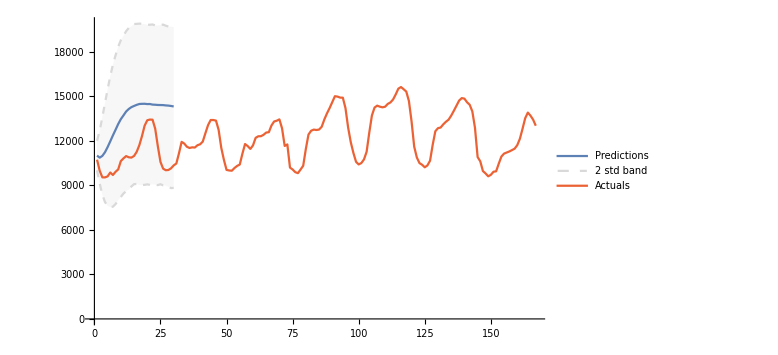

```mathematica
ListLinePlot[{tsModelMedianForecast,tsModelUpperBandForecast,tsModelLowerBandForecast,valuesTest},PlotStyle->{Automatic,Directive[{Dashed,LightGray}],Directive[{Dashed,LightGray}]},Filling->{2->{1},3->{1}},PlotLegends->{"Predictions","2 std band",None,"Actuals"},ImageSize->Large]
```